```mathematica
pete=CoefficientList[(x+x^2+x^3+x^4)^9,x];colin=CoefficientList[(x+x^2+x^3+x^4+x^5+x^6)^6,x];
pete=Rest[pete/Total[pete]];colin=Rest[colin/Total[colin]];
```

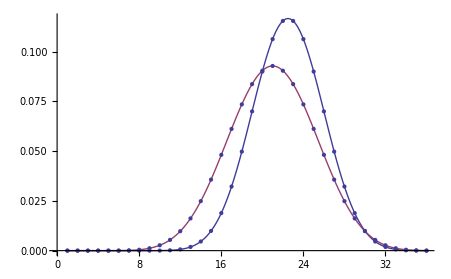

```mathematica
ListPlot[{pete,colin},Joined->True,InterpolationOrder->3,Mesh->Full]
```

```mathematica
Prepend[Accumulate[colin],0]
```

{0,0,0,0,0,0,1/46656,7/46656,7/11664,7/3888,35/7776,77/7776,17/864,31/864,35/576,4501/46656,1687/11664,2401/11664,4345/15552,5647/15552,3527/7776,4249/7776,9905/15552,11207/15552,9263/11664,9977/11664,42155/46656,541/576,833/864,847/864,7699/7776,7741/7776,3881/3888,11657/11664,46649/46656,46655/46656,1}

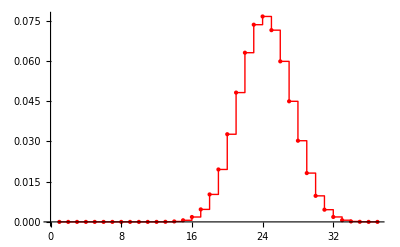

```mathematica
ListPlot[Prepend[Accumulate[colin],0]Append[pete,0],InterpolationOrder->0,Joined->True,Mesh->Full,PlotStyle->Red]
```

```mathematica
Total[Prepend[Accumulate[colin],0]Append[pete,0]]
```

48679795/84934656

```mathematica
N[48679795/84934656,7]
```

0.5731441